```mathematica
f[x_,y_,z_]:={x,y,}
```

```mathematica
scale=40;
radius=0.75;
numPoints=24;
gridSteps=5;
range = 1;
```

```mathematica
(*Print[Table[y/.Solve[x^2+y^2==1],{x,-1,1}]];*)
Plot3D[{x,y,z}/.Solve[x^2+y^2==1],{x,-1,1},{z,0,1},AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
z=0;
ConvertToLevel[a_]:={a[[1]],a[[2]],z};
circle=Table[y /.Solve[x^2+y^2==1],{x,-5,5}];
circle=Map[ConvertToLevel,circle];
Print[circle];
ListPlot3D[circle];
```

{{-2 ⅈ √6,2 ⅈ √6,0},{-ⅈ √15,ⅈ √15,0},{-2 ⅈ √2,2 ⅈ √2,0},{-ⅈ √3,ⅈ √3,0},{0,0,0},{-1,1,0},{0,0,0},{-ⅈ √3,ⅈ √3,0},{-2 ⅈ √2,2 ⅈ √2,0},{-ⅈ √15,ⅈ √15,0},{-2 ⅈ √6,2 ⅈ √6,0}}

```mathematica
scale=40;
radius=0.75;
numPoints=24;
gridSteps=5;
range = 1;
curvesU=Table[scale*f[x,i],{i,-range,range,2/gridSteps}];
curvesV=Table[scale*f[j,y],{j,-range,range,2/gridSteps}];
tubesU=ParametricPlot3D[curvesU,{x,-range,range},PlotStyle->Tube[radius,PlotPoints->numPoints],PlotRange->All];
tubesV=ParametricPlot3D[curvesV,{y,-range,range},PlotStyle->Tube[radius,PlotPoints->numPoints],PlotRange->All];
corners=Graphics3D[Table[Sphere[scale f[i,j],radius],{i,-range,range},{j,-range,range}],PlotPoints->numPoints];
output=Show[tubesU,tubesV,corners]
```

{{40 x,-40,40 (1+x^2)},{40 x,-24,40 (9/25+x^2)},{40 x,-8,40 (1/25+x^2)},{40 x,8,40 (1/25+x^2)},{40 x,24,40 (9/25+x^2)},{40 x,40,40 (1+x^2)}}

-Graphics3D-

```mathematica
ContourPlot[x^2+y^2,{x,-5,5},{y,-5,5},ContourShading->False,Contours->{4,9,16,25},ContourLabels->(Text[Style[Sqrt[#3],20],{#1,#2}]&)];
```

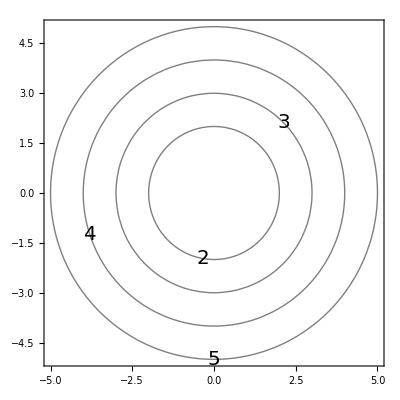

```mathematica
%553
```

```mathematica
equation[x_,y_] := Sqrt[x^2-y^2+10];

range = 10;
plot = Plot3D[equation[x,y],{x,-range,range},{y,-range,range},MeshFunctions->(#3&),Mesh->{Table[{j},{j,-range,range}]},BoxRatios->{1,1,1},MeshStyle->{Thick,Red}]
output = Show[plot];
Export["/Users/Henry/Documents/ProjectProject/mathematica/exports/saddle_levelcurve.stl",output];
```

-Graphics3D-

```mathematica
equation[x_,y_] := Sqrt[x+y^2];

cp=ContourPlot[equation[x,y],{x,-5,5},{y,-5,5},Frame->False,Axes->False,PlotRangePadding->0,Contours->{4,9,16,25},ContourShading->False];
p1=Plot3D[equation[x,y],{x,-5,5},{y,-5,5},MeshFunctions->(#3&),Mesh->{Table[{j},{j,2,5}]},BoxRatios->{1,1,1},MeshStyle->{Thick,Red}];




level=-1.2 10^-8;gr=Graphics3D[{Texture[cp],EdgeForm[],Polygon[{{-5,-5,level},{5,-5,level},{5,5,level},{-5,5,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];
output=Show[p1,gr];
Export["/Users/Henry/Documents/ProjectProject/mathematica/exports/other_levelcurve.stl",output];
```